```mathematica
(* new equations, with conformal maps  we set κ =1, q =1*)
```

```mathematica
LHS =  r' + I λ'
```

r'+ⅈ λ'

```mathematica
RHS = -2 I (E^(-2I λ) + p E^(-4I λ))/ R
```

-(2 ⅈ (ⅇ^(-2 ⅈ λ)+ⅇ^(-4 ⅈ λ) p))/R

```mathematica
Eqc =FullSimplify[ComplexExpand[ReIm[LHS == RHS]],{λ,r, λ', r'} ϵ Reals]
```

{r'==-(2 (Sin[2 λ]+p Sin[4 λ]))/R,λ'==-(2 (Cos[2 λ]+p Cos[4 λ]))/R}

```mathematica
(* try direct approach *)
SubAll = #->#[θ]& /@{r,λ,r',λ',R,R'}
```

{r→r[θ],λ→λ[θ],r'→r'[θ],λ'→λ'[θ],R→R[θ],R'→R'[θ]}

```mathematica
Eqc
```

{r'==-(2 (Sin[2 λ]+p Sin[4 λ]))/R,λ'==-(2 (Cos[2 λ]+p Cos[4 λ]))/R}

```mathematica
EQAll = Append[Eqc,R' ==-R Cot[θ + λ]]
```

{r'==-(2 (Sin[2 λ]+p Sin[4 λ]))/R,λ'==-(2 (Cos[2 λ]+p Cos[4 λ]))/R,R'==-R Cot[θ+λ]}

```mathematica
DSolve[{λ'[θ]==-(2 (Cos[2 λ[θ]]+p Cos[4 λ[θ]]))/R[θ],R'[θ]==-R[θ] Cot[θ+λ[θ]]},{λ[θ],R[θ]}, θ]
```

DSolve[{λ'[θ]==-(2 (Cos[2 λ[θ]]+p Cos[4 λ[θ]]))/R[θ],R'[θ]==-Cot[θ+λ[θ]] R[θ]},{λ[θ],R[θ]},θ]

```mathematica
Simplify[(w/.Solve[w + p (2 w^2-1)==0,w][[2]])(1+√(1+8 p^2))]/(1+√(1+8 p^2))
```

```mathematica
Sqrt[(1 +(2 p)/(1+√(1+8 p^2)))/2]//Simplify
```

√(1/2+p/(1+√(1+8 p^2)))

```mathematica
f[λ_] := Cos[2 λ]+p Cos[4 λ];
```

```mathematica
FullSimplify[Cos[λ]/.Solve[f[λ] ==0,λ],-1 -p > 0]/.C[1]->0
```

{(√(-(1-4 p+√(1+8 p^2))/p))/(2 √2),(√(-(1-4 p+√(1+8 p^2))/p))/(2 √2),Cos[1/2 ArcTan[1-√(1+8 p^2),-√2 √(-1+4 p^2+√(1+8 p^2))]],Cos[1/2 ArcTan[1-√(1+8 p^2),√2 √(-1+4 p^2+√(1+8 p^2))]]}

```mathematica
Eqλ2=Simplify[λ''[θ] -λ'[θ]((f'[λ]/f[λ])/.{λ->λ[θ]}) λ'[θ] ]== λ'[θ]Cot[θ+λ[θ]]
```

(2 (Sin[2 λ[θ]]+2 p Sin[4 λ[θ]]) λ'[θ]^2)/(Cos[2 λ[θ]]+p Cos[4 λ[θ]])+λ''[θ]==Cot[θ+λ[θ]] λ'[θ]

```mathematica
ClearAll[λ,R];
```

```mathematica
dsol[p0_,ϵ_]:=NDSolve[
{Eqλ2/.{p->p0},
R'[θ]==-R[θ] Cot[θ+λ[θ]],
λ[ϵ]== Pi/2, 
λ[Pi/4-ϵ]==ArcCos[√(1/2+p0/(1+√(1+8 p0^2)))],
 R[ϵ]==1},
{λ[θ],R[θ]},{θ,ϵ,Pi/4 -ϵ}][[1]];
```

```mathematica
ss = dsol[-0.01,0.0001]
```

{λ[θ]→InterpolatingFunction[…][θ],R[θ]→InterpolatingFunction[…][θ]}

```mathematica
SubTau[F_,ε_] := (F/.ss)/.θ->If[Abs[τ] < Pi/2,Abs[τ],Pi -Abs[τ]]+ε;
```

InterpolatingFunction::dmval: Input value {1.57073} lies outside the range of data in the interpolating function. Extrapolation will be used.

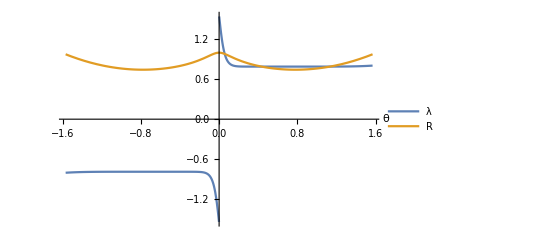

```mathematica
With[{ϵ=0.001},
Plot[ {Sign[Sin[τ]]SubTau[λ[θ],ϵ],SubTau[R[θ],ϵ]},{τ,-(Pi/2 -ϵ),Pi/2 -ϵ},
PlotRange->All,AxesLabel->{θ,None},PlotLegends->{λ,R}]]
```

```mathematica
|
```

```mathematica
Plt[dir_]:=Module[{ε=0.001},
ParametricPlot[With[{r = SubTau[R[θ],ε]},{dir r Cos[τ],r Sin[τ]}],{τ,-Pi/2 +ε,Pi/2-ε},PlotLabel->x+I y == ℂ[θ]]]
```

InterpolatingFunction::dmval: Input value {1.57073} lies outside the range of data in the interpolating function. Extrapolation will be used.

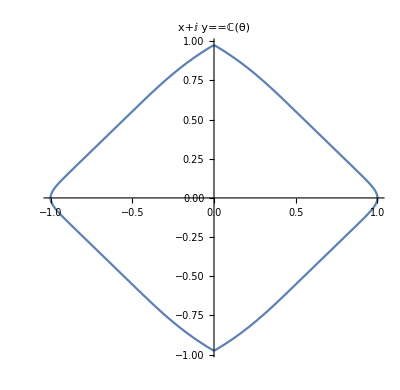

```mathematica
Show[{Plt[-1],Plt[1]},PlotRange->All]
```

```mathematica
RCross[p_?NumericQ,r0_?NumericQ] := With[{ϵ=0.001},((R[θ]/.dsol[p,r0,ϵ])/.θ->Pi/4 -ϵ)]
```

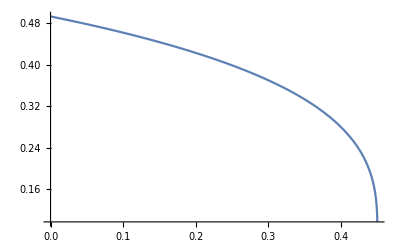

```mathematica
Plot[RCross[-0.25,r0],{r0,0.,0.45}]
```

```mathematica
FindRoot[RCross[-0.25,r0],{r0,0.44}]
```

NDSolve::ndinnt: Initial condition r0 is not a number or a rectangular array of numbers.

ReplaceAll::reps: {r'[θ]==-(2 ⅇ^r[θ] (Sin[2 λ[θ]]-0.25 Sin[4 λ[«1»]]))/R[θ],λ'[θ]==-(2 ⅇ^r[θ] (Cos[2 λ[θ]]-0.25 Cos[4 λ[«1»]]))/R[θ],R'[θ]==-Cot[θ+λ[θ]] R[θ],λ[0.001]==π/4,r[0.001]==r0,R[0.001]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {r'[0.784398]==-(2 ⅇ^r[0.784398] (Sin[2 λ[0.784398]]-0.25 Sin[4 λ[«1»]]))/R[0.784398],«4»,R[0.001]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {r'[0.784398]==-(2 ⅇ^r[0.784398] (Sin[2 λ[0.784398]]-0.25 Sin[4 λ[«1»]]))/R[0.784398],λ'[0.784398]==-(2 ⅇ^(«1») (Cos[2 λ[0.784398]]-0.25 Cos[4 λ[«1»]]))/R[0.784398],R'[0.784398]==-«1» «1»,«1»,r[0.001]==0.44,R[0.001]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {R[0.784398]/.{r'[0.784398]==-(2. 2.71828^r[0.784398] (Sin[Times[«2»]]-0.25 Sin[«1»]))/R[0.784398],λ'[0.784398]==-(2. («18»)^(«1») (Cos[Times[«2»]]-0.25 Cos[«1»]))/R[0.784398],R'[«19»]==«1»,«1»,r[0.001]==0.44,R[0.001]==1.}} is not a list of numbers with dimensions {1} at {r0} = {0.44}.

FindRoot[RCross[-0.25,r0],{r0,0.44}]